# Homework 6 Erik Worth

## 1.

```mathematica
200!
```

788657867364790503552363213932185062295135977687173263294742533244359449963403342920304284011984623904177212138919638830257642790242637105061926624952829931113462857270763317237396988943922445621451664240254033291864131227428294853277524242407573903240321257405579568660226031904170324062351700858796178922222789623703897374720000000000000000000000000000000000000000000000000

## 2.

```mathematica
50000! // N
```

3.34732050959714×10^213236

## 3.

```mathematica
Code:

#include <stdio.h>
#include <math.h>
#define e 2.71828182845904523536028747135266249775724709369995

main()
{
	int N = 50000, i;
	double fact, sum = 0;
	
	for ( i = 1; i < N + 1; ++i)
	{
		sum += log(i);
		
	}
	
	printf("sum = %f\n", sum);
	printf("ans = %f^%f", e, sum);
}

Output:

sum = 490995.243050
ans = 2.718282^490995.243050
```

In a for loop, log(i) is added iteratively to the variable sum, from i = 1 to 50000. So at the end sum is log(N) + log(N-1) + ... + log(1), or log(N!). The answer is expressed as e to the power of log(N!).

## 4.

```mathematica
AccountingForm[Exp[Pi Sqrt[163.]], 15]
```

AccountingForm::sigz: In addition to the number of digits requested, one or more zeros will appear as placeholders.

262537412640768000.

```mathematica
AccountingForm[Exp[Pi Sqrt[163.]], 16]
```

AccountingForm::sigz: In addition to the number of digits requested, one or more zeros will appear as placeholders.

262537412640768200.

```mathematica
AccountingForm[Exp[Pi Sqrt[163.]], 17]
```

AccountingForm::sigz: In addition to the number of digits requested, one or more zeros will appear as placeholders.

262537412640768200.

AccountingForm stops giving additional digits at 17, so it must take 16 digits to express the answer as an integer.

## 5.

```mathematica
NSolve[ x^7 + x^5 + 2 x^3 + x^2 + 1 == 0, {x}]
```

{{x→-0.812432},{x→-0.640787-1.07931 ⅈ},{x→-0.640787+1.07931 ⅈ},{x→0.254825-0.700968 ⅈ},{x→0.254825+0.700968 ⅈ},{x→0.792178-0.881387 ⅈ},{x→0.792178+0.881387 ⅈ}}

NSolve solves the equation and gives 7 solutions for x, 1 real and 6 complex.

## 6.

```mathematica
NIntegrate[HermiteH[4,x]^2 Exp[-x^2], {x, -Infinity, Infinity}]
```

680.622

NIntegrate numerically solves the given integral and returns 680.622 to 6 significant figures.

## 7.

```mathematica
sol = NDSolve[{y''[x] == 2x + y[x] + 3y'[x], y[2] ==1, y'[2] == -1}, y, {x, 2, 2.3}]
```

{{y→InterpolatingFunction[{{2.,2.3}},<>]}}

```mathematica
y[2.2] /. sol
```

{0.851094}

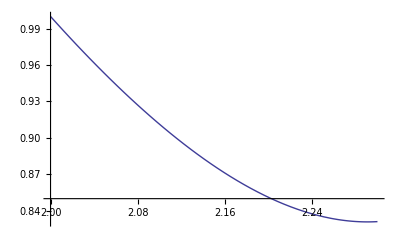

```mathematica
Plot[y[x] /. sol, {x, 2.0, 2.3}]
```

The given equation is solved numerically with NDSolve for the boundary conditions supplied. The answer is stored in sol, and is evaluated at x = 2.2 with the replacement operator. y[x] is then plotted from x = 2 to x = 2.3, again using the replacement operator.

## 8.

```mathematica
Solve[{4x + 5y == 5, 6x + 7y == 7}, {x,y}]
```

{{x→0,y→1}}

The given simultaneous equations are solved analytically with Solve, and the answer given is x = 0, y = 1.

## 9.

```mathematica
Solve[Sqrt[x + 2] + 4 == x, x]
```

{{x→7}}

Solve finds x = 7 by analytically solving the given equation.

## 10.

```mathematica
Limit[1/(Exp[x]-Exp[x-x^-2]), x -> Infinity]
```

0

The function Limit produces the answer of 0 for the given function.

## 11.

```mathematica
DSolve[y''[x] - 6y'[x] + 13y[x] == Exp[x]Cos[x], y[x], x]
```

{{y[x]→ⅇ^(3 x) C[2] Cos[2 x]+ⅇ^(3 x) C[1] Sin[2 x]+1/260 ⅇ^x (13 Cos[x] Cos[2 x]+15 Cos[2 x] Cos[3 x]+26 Cos[2 x] Sin[x]-26 Cos[x] Sin[2 x]-10 Cos[3 x] Sin[2 x]+13 Sin[x] Sin[2 x]+10 Cos[2 x] Sin[3 x]+15 Sin[2 x] Sin[3 x])}}

DSolve is used to analytically solve the given differential equation. The general solution includes arbitrary constants C[1] and C[2] since no boundary conditions are given.

## 12.

a)

```mathematica
xlist = {0, 1, 2, 3, 4, 5, 6, 7, 8, 9, 10}
```

{0,1,2,3,4,5,6,7,8,9,10}

b)

```mathematica
ylist = xlist^2
```

{0,1,4,9,16,25,36,49,64,81,100}

c)

```mathematica
mylist =Transpose[{xlist, ylist}]
```

{{0,0},{1,1},{2,4},{3,9},{4,16},{5,25},{6,36},{7,49},{8,64},{9,81},{10,100}}

d)

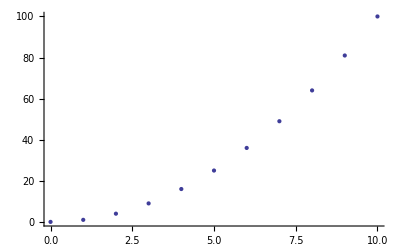

```mathematica
ListPlot[mylist]
```

xlist is a list of the integers from 0 to 10. ylist is a list those integers squared. A list called mylist is defined as the transpose of {xlist, ylist}, which produces a list of ordered pairs (xlist[i], ylist[i]). Then ListPlot is used to plot mylist.

## 13.

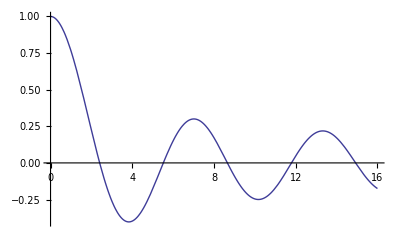

```mathematica
Plot[BesselJ[0,x], {x, 0, 16}]
```

```mathematica
FindRoot[BesselJ[0,x], {x,  2}] FindRoot[BesselJ[0,x], {x,  5}]FindRoot[BesselJ[0,x], {x,  10}]FindRoot[BesselJ[0,x], {x,  12}]FindRoot[BesselJ[0,x], {x,  15}]
```

{(x→2.40483) (x→5.52008) (x→8.65373) (x→11.7915) (x→14.9309)}

The given Bessel function is plotted to get an idea for the roots, then FindRoot is used five times to find the roots at different values of x. The answer is supplied in a series of replacement rules.

## 14.

a)

```mathematica
u[x_, n_]:=2^(-n/2)((n!)^-0.5)((1/Pi)^0.25)HermiteH[n, x]Exp[-x^2/2]
```

```mathematica
Integrate[u[x, 3]^2, {x, -Infinity, Infinity}]
```

1.

b)

```mathematica
Integrate[u[x,3]u[x,2], {x, -Infinity, Infinity}]
```

0

c)

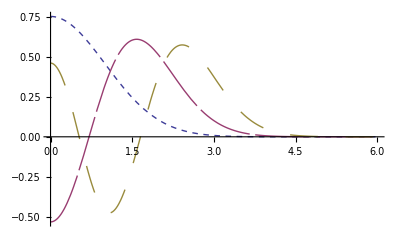

```mathematica
Plot[{u[x,0], u[x, 2], u[x,4]}, {x, 0, 6}, PlotStyle -> {Dashing[{0.01, 0.01}], Dashing[{0.1,0.01}], Dashing[{0.05, 0.05}]}]
```

The given function is defined as the function u[x.n] where √(ℏ/(𝓂ω)) and its reciprocal are equal to 1. u[x.3] is squared and integrated analytically and the solution given is 1. Then u[x.2]u[x3] is integrated analytically and the answer is 0. Next u[x,0], u[x,2] and u[x.4] are plotted on the same graph from x = 0 to x = 6 with three different dashing styles.

## 15.

a)

```mathematica
s = NDSolve[{i'[t]+2i[t]==Sin[t], i[0] == 0}, i, {t, 0, 1.1}]
```

{{i→InterpolatingFunction[{{0.,1.1}},<>]}}

```mathematica
ansN[t_] := i[t]/.s[[1]]
```

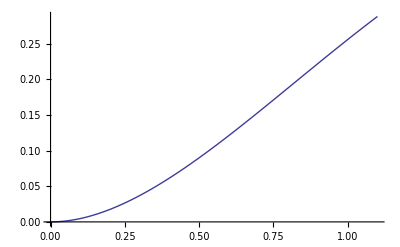

```mathematica
Plot[i[t] /. s, {t, 0, 1.1}]
```

b)

```mathematica
s2 =DSolve[{2 i[t]+i'[t]==Sin[t],i[0]==0},i[t],t]
```

{{i[t]→-1/5 ⅇ^(-2 t) (-1+ⅇ^(2 t) Cos[t]-2 ⅇ^(2 t) Sin[t])}}

```mathematica
ansA[t_] := i[t] /. s2[[1]]
```

```mathematica
Plot[i[t] /. s2, {t, 0, 1.1}]
```

-Graphics-

c)

```mathematica
nlist = Table[ansN[t], {t, 0, 1, 0.1}]
```

{0.,0.0046787,0.0175184,0.0369031,0.0614209,0.0898296,0.121029,0.154038,0.18798,0.222069,0.255595}

```mathematica
alist = Table[ansA[t], {t, 0, 1, 0.1}]
```

{0.,0.00467868,0.0175184,0.0369031,0.0614209,0.0898296,0.121029,0.154038,0.18798,0.222069,0.255595}

```mathematica
TableForm[Transpose[{nlist, alist}], TableHeadings -> {None, {"Numeric", "Analytic"}}]
```

Numeric | Analytic
0. | 0.
0.0046787 | 0.00467868
0.0175184 | 0.0175184
0.0369031 | 0.0369031
0.0614209 | 0.0614209
0.0898296 | 0.0898296
0.121029 | 0.121029
0.154038 | 0.154038
0.18798 | 0.18798
0.222069 | 0.222069
0.255595 | 0.255595

In part a) the ODE is solved using NDSolve and the answer is stored as a function in ansN[t] and plotted to get a sense of what it looks like. In part b) DSolve is used to solve the ODE analytically and a real function is returned, stored in ansA[t] and plotted. In c) the functions are evaluated from 0 to 1 in steps of 0.1, and the results are stored in two lists. The two lists are transposed and TableForm makes a table of the results.